```mathematica
Ori=Import["G:\\毕个业\\basic\\pack\\pack12\\Ori.csv"];
Rc=Import["G:\\毕个业\\basic\\pack\\pack12\\Rc.csv"];
CyList=Range[Dimensions[Rc][[2]]];
CyFigList=Range[Dimensions[Rc][[2]]];
d=30.4*2;
h=4.7*2;

For[i=1,i<=Dimensions[Rc][[2]],i++,
startP=Rc[[All,i]]-   Ori[[All,i]]*h/2;
endP=Rc[[All,i]]+    Ori[[All,i]]*h/2;
CyList[[i]]=Cylinder[{startP,endP},d/2]
];
For[i=1,i<=Dimensions[Rc][[2]],i++,CyFigList[[i]]=Graphics3D[CyList[[i]]]];
Show[CyFigList]
cav=RegionUnion[CyList];
```

-Graphics3D-

```mathematica
minX=Min[Rc[[1]]]+d;maxX= Max[Rc[[1]]]-d;
minY= Min[Rc[[2]]]+d;maxY= Max[Rc[[2]]]-d;
minZ=Min[Rc[[3]]]+d;maxZ= Max[Rc[[3]]]-d;
testnum=1000;
MinDisList=Range[testnum];
MinDisTmpList=Range[Dimensions[Rc][[2]]];
Parallelize[
For[i=1,i<=testnum,i++,
x=RandomReal[{minX,maxX}];y=RandomReal[{minY,maxY}];z=RandomReal[{minZ,maxZ}];

For[j=1,j<=Dimensions[Rc][[2]],j++,
MinDisTmpList[[j]]=RegionDistance[CyList[[j]],{x,y,z}]
];
MinDisList[[i]]=Min[MinDisTmpList];
];
];
MinDisList=Delete[MinDisList, Position[Chop[MinDisList],0]];
Histogram[MinDisList];
```

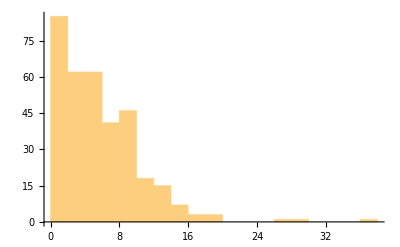

```mathematica
minX=Min[Rc[[1]]]+d;maxX= Max[Rc[[1]]]-d;
minY= Min[Rc[[2]]]+d;maxY= Max[Rc[[2]]]-d;
minZ=Min[Rc[[3]]]+d;maxZ= Max[Rc[[3]]]-d;
testnum=1000;
lengthRatioList=Range[testnum];
ReTmpList=Range[Dimensions[Rc][[2]]];
For[i=1,i<=testnum,i++,
x1=RandomReal[{minX,maxX}];y1=RandomReal[{minY,maxY}];z1=RandomReal[{minZ,maxZ}];
x2=RandomReal[{minX,maxX}];y2=RandomReal[{minY,maxY}];z2=RandomReal[{minZ,maxZ}];

p1={x1,y1,z1};p2={x2,y2,z2};
v12=p2-p1;
line1=Line[{p1,p2}];
For[j=1,j<=Dimensions[Rc][[2]],j++,
p0=Rc[[All,j]];
v10=p0-p1;
dis=Sin[VectorAngle[v12,v10]]*Norm[v10];
If[dis<d,
ReTmpList[[j]]=RegionIntersection[line1,CyList[[j]]],
ReTmpList[[j]]=EmptyRegion[3];
];
];
re=RegionUnion[ReTmpList];
lengthRatioList[[i]]=RegionMeasure[re]/(√((x2-x1)^2+(y2-y1)^2+(z2-z1)^2));
Show[Region[re]]
];
lengthRatioList=Delete[lengthRatioList, Position[Chop[lengthRatioList],0]];
Histogram[lengthRatioList];
```

```mathematica
minX=Min[Rc[[1]]]+d;maxX= Max[Rc[[1]]]-d;
minY= Min[Rc[[2]]]+d;maxY= Max[Rc[[2]]]-d;
minZ=Min[Rc[[3]]]+d;maxZ= Max[Rc[[3]]]-d;
```